ORIGINAL ARTICLE: Adam Cieślik, Eva Hackmann, and Patryk Mach: Kerr geodesics in terms of Weierstrass elliptic functions,  Phys. Rev. D 108, 024056 (2023), DOI: https://doi.org/10.1103/PhysRevD.108.024056

## Introduction

Our paper introduces new general solutions to the Kerr geodesic equations in Boyer-Lindquist coordinates. These solutions are analytic and describe timelike and null geodesics in the Kerr spacetime. The solutions are explicitly parametrized by constants of motion, such as energy, angular momentum, and the Carter constant, along with initial coordinates. To simplify the usage of all the functions described in the paper, we have developed the KerrEqOfMotGeneral.wl package. In this notebook, I will demonstrate how to use it.

## Install package

To use the KerrEqOfMotGeneral.wl package file in Mathematica, simply place it in the same directory as your notebook. Then, load the package using the below functions.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<"KerrEqOfMotGeneral.wl"
```

## About functions in package

This package provides  general solutions of the Kerr geodesic equations in Boyer-Lindquist coordinates. They are given by the following functions
	- ξ[s,{ϵ_r,ξ_0,ε,κ,λ_z,α,δ}] - radial distance;
	- θ[s,{ϵ_θ,θ_0,ε,κ,λ_z,α,δ}] - polar coordinate;
	- φ[s,{φ_0,ϵ_r,ξ_0,ϵ_θ,θ_0,ε,κ,λ_z,α,δ}] - azimuthal coordinate;
	- Τ[s,{Τ_0,ϵ_r,ξ_0,ϵ_θ,θ_0,ε,κ,λ_z,α,δ}] - time coordinate;

In order to obtain a complete description of a particular function, write:

```mathematica
?ξ
```

In addition to solutions to the equations of motion, the package also contains all integrals appearing in the work encoded, for example

```mathematica
?I1
```

```mathematica
?I25
```

```mathematica
?K3
```

```mathematica
?L3
```

The package offers more features, such as

```mathematica
?θmax
```

```mathematica
?θmin
```

```mathematica
?Fancylog
```

## Basic Examples

Presenting a particle motion for given initial data is easy

```mathematica
ϕ00=0.33;ϵr=-1;r00=10;ϵth=+1;th00=0.85;ϵ=Sqrt[0.95];λz=3;a=0.8;κ=12;δ=1;
```

Locations of Kerr horizons

```mathematica
rhin=1-√(1-a^2);rhout=1+√(1-a^2);
```

#### Motion in the X-Y plane

Let us plot the motion in the X-Y plane

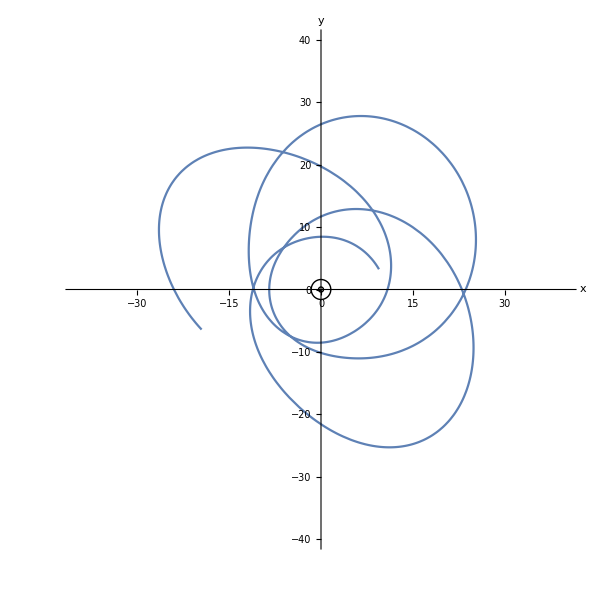

```mathematica
ParametricPlot[{ξ[s,{ϵr,r00,ϵ,κ,λz,a,δ}]Cos[φ[s,{ϕ00,ϵr,r00,ϵth,th00,ϵ, κ, λz,a, δ}]],ξ[s,{ϵr,r00,ϵ,κ,λz,a,δ}]Sin[φ[s,{ϕ00,ϵr,r00,ϵth,th00,ϵ, κ, λz,a, δ}]]},{s,0,5.35},PlotRange->{{-40,40},{-40,40}},Epilog->{Circle[{0,0},rhin],Circle[{0,0},rhout]},ImageSize->600,AxesLabel->{"x","y"}]
```

#### Motion in the X-Z plane

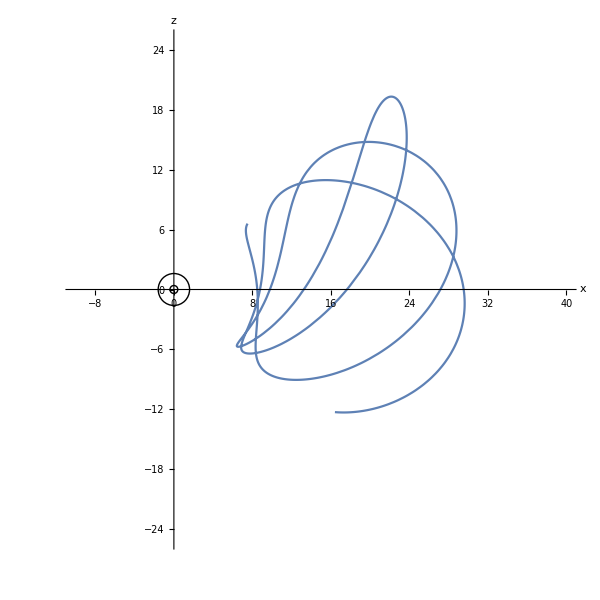

```mathematica
ParametricPlot[{ξ[s,{ϵr,r00,ϵ,κ,λz,a,δ}]Sin[θ[s,{ϵth,th00,ϵ, κ, λz,a, δ}]],ξ[s,{ϵr,r00,ϵ,κ,λz,a,δ}]Cos[θ[s,{ϵth,th00,ϵ, κ, λz,a, δ}]]},{s,0,5.35},PlotRange->{{-10,40},{-25,25}},Epilog->{Circle[{0,0},rhin],Circle[{0,0},rhout]},ImageSize->600,
AxesLabel->{"x","z"}]
```

#### Marking the constraints

We can see that movement is restricted in θ. Using the θmax and θmin functions, we can draw these constraints.

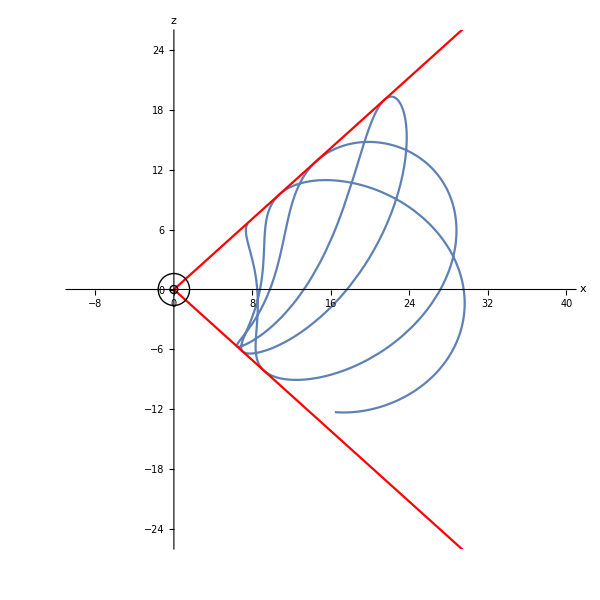

```mathematica
Show[
ParametricPlot[{ξ[s,{ϵr,r00,ϵ,κ,λz,a,δ}]Sin[θ[s,{ϵth,th00,ϵ, κ, λz,a, δ}]],ξ[s,{ϵr,r00,ϵ,κ,λz,a,δ}]Cos[θ[s,{ϵth,th00,ϵ, κ, λz,a, δ}]]},{s,0,5.35},PlotRange->{{-10,40},{-25,25}},Epilog->{Circle[{0,0},rhin],Circle[{0,0},rhout]},ImageSize->600,
AxesLabel->{"x","z"}],
Plot[Tan[Pi/2-θmin[ϵth,th00,ϵ, κ, λz,a, δ]]*x,{x,0,30},PlotStyle->Red],
Plot[Tan[Pi/2-θmax[ϵth,th00,ϵ, κ, λz,a, δ]]*x,{x,0,30},PlotStyle->Red]
]
```

#### Dynamic evolution

In the case of movement in the X-Z plane, we can easily create a dynamic evolution with the change of the parameter s - Mino time. For motion in the X-Y plane, it is also feasible but considerably slower, as the φ coordinate relies on the complex logarithm derived from the ratio of two Weierstrass special functions. A more detailed explanation of this phenomenon can be found in the last section of this notebook.

First, we need to set some initial value of the parameter that we will change

```mathematica
ss=0.1;
```

Next, we create a slider that we will manipulate. We can also consider negative values of the Mino time, in other words, movement backwards in time.

```mathematica
Slider[Dynamic[ss],{-5.35,5.35}]
```

Now, by changing the slider, we can see how the particle’s position changes in the plot below.

```mathematica
Dynamic[Show[
ParametricPlot[{ξ[s,{ϵr,r00,ϵ,κ,λz,a,δ}]Sin[θ[s,{ϵth,th00,ϵ, κ, λz,a, δ}]],ξ[s,{ϵr,r00,ϵ,κ,λz,a,δ}]Cos[θ[s,{ϵth,th00,ϵ, κ, λz,a, δ}]]},{s,0,ss},PlotRange->{{-10,40},{-25,25}},Epilog->{Circle[{0,0},rhin],Circle[{0,0},rhout]},ImageSize->600,
AxesLabel->{"x","z"}],
Plot[Tan[Pi/2-θmin[ϵth,th00,ϵ, κ, λz,a, δ]]*x,{x,0,30},PlotStyle->Red],
Plot[Tan[Pi/2-θmax[ϵth,th00,ϵ, κ, λz,a, δ]]*x,{x,0,30},PlotStyle->Red]
]]
```

#### 3D plot

We can create a 3D plot with a sphere at the center, which has the external horizon’s radius for simplicity.

```mathematica
Show[ParametricPlot3D[{ξ[s,{ϵr,r00,ϵ,κ,λz,a,δ}]Sin[θ[s,{ϵth,th00,ϵ, κ, λz,a, δ}]]Cos[φ[s,{ϕ00,ϵr,r00,ϵth,th00,ϵ, κ, λz,a, δ}]],ξ[s,{ϵr,r00,ϵ,κ,λz,a,δ}]Sin[θ[s,{ϵth,th00,ϵ, κ, λz,a, δ}]]Sin[φ[s,{ϕ00,ϵr,r00,ϵth,th00,ϵ, κ, λz,a, δ}]],ξ[s,{ϵr,r00,ϵ,κ,λz,a,δ}]Cos[θ[s,{ϵth,th00,ϵ, κ, λz,a, δ}]]},{s,0,5.35},PlotRange->3{{-10,10},{-10,10},{-10,10}},ImageSize->600,AxesLabel->{"x","y","z"}],SphericalPlot3D[rhout,{θ,0,Pi},{ϕ,0,2Pi}]]
```

-Graphics3D-

#### Proper time

The above functions are parametrized by the Mino time s. The package offers a function which convert Mino's time to the proper time τ̃:
					τ̃=M/m tildτ[s,{tildτ_0,ϵ_r,ξ_0,ϵ_θ,θ_0,ε,κ,λ_z,α,δ}],
where:
 - tildτ[s,{tildτ_0,ϵ_r,ξ_0,ϵ_θ,θ_0,ε,κ,λ_z,α,δ}] - returns a value of the affine parameter;
	- M - black hole mass;
	- m - particle mas;

We can check how the coordinate time depends on the proper time

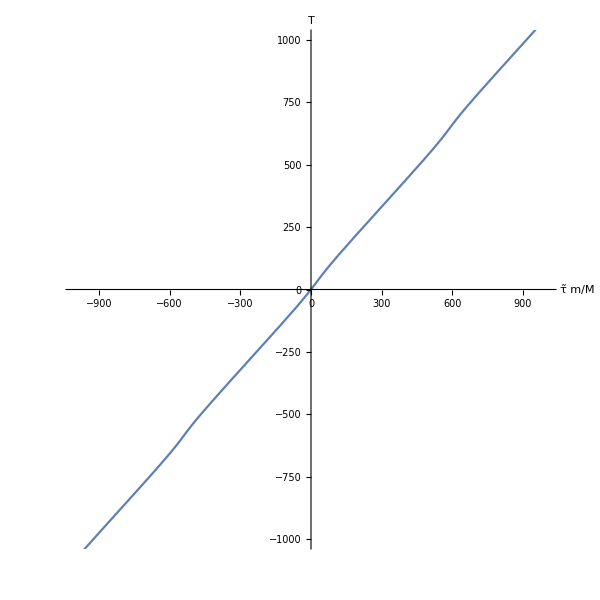

```mathematica
ParametricPlot[{tildτ[s,{ 0,ϵr, r00, ϵth, th00, ϵ, κ, λz, a, δ}],Τ[s,{0, ϵr, r00,  ϵth, th00, ϵ, κ, λz, a, δ}]},{s,-3,3.5},PlotRange->{{-1000,1000},{-1000,1000}},ImageSize->600,AxesLabel->{"τ̃ m/M","Τ"}]
```

## Fancylog

When analyzing the computational speed of the functions ξ, θ, and φ, Τ a significant difference is noticeable. This is because the latter two require a calculation of Log[(σ(s-y;g_2,g_3))/(σ(s+y; g_2, g_3))],  where σ represents the Weierstrass sigma function, with s representing the Mino time and y being a generally complex parameter. Implementing our formulas correctly to obtain continuous solutions for  φ and T, necessitates a meticulous choice of the branch for the complex logarithm. This problem, along with our attempts to solve it, is thoroughly described in our work. 
The new formula for the logarithm is encoded as a function Fancylog. Below is a simple example where you can see the differences between the two definitions of logarithm

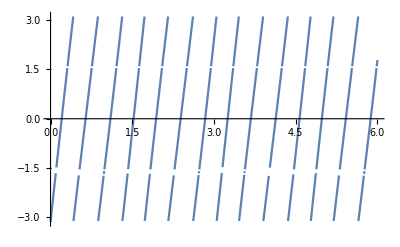

```mathematica
Plot[Im[Log[WeierstrassSigma[s-(19+5.3I),{29.5,0.55}]/WeierstrassSigma[s+19+5.3I,{29.5,0.55}]]],{s,0,6}]
```

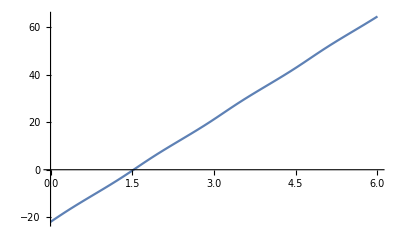

```mathematica
Plot[Im[Fancylog[s,19+5.3I,{29.5,0.55}]],{s,0,6}]
```

## Conclusion

We’ve designed this package with the intention of providing utmost usefulness to our users. However, we acknowledge that there is always scope for improvement in our code. To make Fancylog faster, we are planning to upgrade its definition in the near future. We welcome any feedback or suggestions you may have, you can write to me here or in the comments.